(15 √3)/2

15/2

π/6

π/6

π/6

«10 more identical outputs»

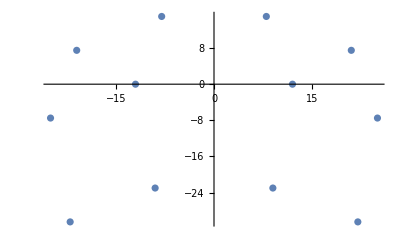

```mathematica
(*
X0 = 50+12.5;
Y0 = 900;

X1 = 50-12.5;
Y1 = 900;

X2 = 50+8;
Y2 = 900+15;

X3 = 50-8;
Y3 = 900+15;

X4 = 50+9;
Y4 = 900-13;

X5 = 50-9;
Y5 = 900-13;
*)

X0 = -8;
Y0 = 15;

X1 = 8;
Y1 = 15;

X2 = 12;
Y2 = 0;

X3 = 9;
Y3 = -23;

X4 = -9;
Y4 = -23;

X5 = -12;
Y5 = 0;

X6 = 0;
Y6 = 0;



FootX0 = X0 - 15 * Cos[Pi/6];
FootY0 = Y0 - 15 *Sin[Pi/6];
FootY0me = Y0 + 15 *Sin[Pi/6];


FootX5 = X5- 15 * Cos[Pi/6];
FootY5 = Y5 - 15 *Sin[Pi/6];
FootY5me = Y5+ 15 *Sin[Pi/6];

FootX4 = X4- 15 * Cos[Pi/6];
FootY4 = Y4 - 15 *Sin[Pi/6];
FootY4me = Y4 + 15 *Sin[Pi/6];

FootX1 = X1+ 15 * Cos[Pi/6];
FootY1 = Y1 - 15 *Sin[Pi/6];
FootY1me = Y1 + 15 *Sin[Pi/6];

 FootX2 = X2+ 15 * Cos[Pi/6];
FootY2 = Y2 - 15 *Sin[Pi/6];
FootY2me = Y2 + 15 *Sin[Pi/6];

FootX3= X3+15 * Cos[Pi/6];
FootY3 = Y3 - 15 *Sin[Pi/6];
FootY3me = Y3 + 15 *Sin[Pi/6];

FootX6= X6+15 * Cos[Pi/6]
FootY6 = Y6 - 15 *Sin[Pi/6];
FootY6me = Y6 + 15 *Sin[Pi/6]

angle0him = -ArcTan[(X0-FootX0),(FootY0-Y0)]
angle4him = -ArcTan[(X4-FootX4),(FootY4-Y4)]
angle5him = -ArcTan[(X5-FootX5),(FootY5-Y5)]

angle1him = -ArcTan[(FootX1-X1),(FootY1-Y1)]
angle2him = -ArcTan[(FootX2-X2),(FootY2-Y2)]
angle3him = -ArcTan[(FootX3-X3),(FootY3-Y3)]


angle0me = ArcTan[(Abs[FootX0]-Abs[X0]),(FootY0me-Y0)]
angle5me = ArcTan[(Abs[FootX5]-Abs[X5]),(FootY5me-Y5)]
angle4me = ArcTan[(Abs[FootX4]-Abs[X4]),(FootY4me-Y4)]

angle1me = ArcTan[(FootX1-X1),(FootY1me-Y1)]
angle2me = ArcTan[(FootX2-X2),(FootY2me-Y2)]
angle3me = ArcTan[(FootX3-X3),(FootY3me-Y3)]

angle6me = ArcTan[(FootX6-X6),(FootY6me-Y6)]


(*angle1me = ArcTan[(FootY1-Y1),(Abs[FootX1]-Abs[X1])]
angle3me = ArcTan[(FootY3-Y3),(Abs[FootX3]-Abs[X3])]
angle5me = ArcTan[(FootY5-Y5),(Abs[FootX5]-Abs[X5])]*)

JointandFoot = ListPlot[{{X0,Y0},{FootX0,FootY0},{X1,Y1},{FootX1,FootY1},{X2,Y2},{FootX2,FootY2},{X3,Y3},{FootX3,FootY3},{X4,Y4},{FootX4,FootY4},{X5,Y5},{FootX5,FootY5}}]
```

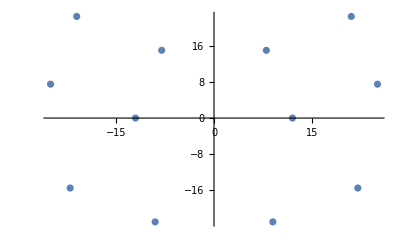

```mathematica
MyJointandFoot = ListPlot[{{X0,Y0},{FootX0,FootY0me},{X1,Y1},{FootX1,FootY1me},{X2,Y2},{FootX2,FootY2me},{X3,Y3},{FootX3,FootY3me},{X4,Y4},{FootX4,FootY4me},{X5,Y5},{FootX5,FootY5me}}]
```

```mathematica
JointPlot =  ListPlot[{{X0,Y0},{X1,Y1},{X2,Y2},{X3,Y3},{X4,Y4},{X5,Y5}}];
```

```mathematica
FootPlot = ListPlot[{{FootX0,FootY0},{FootX1,FootY1},{FootX2,FootY2},{FootX3,FootY3},{FootX4,FootY4},{FootX5,FootY5}}];
```

```mathematica
Show[JointPlot,FootPlot];
```